```mathematica
ClearGlobal[];
```

```mathematica
$Assumptions={ {Lx, Ly, Lz}∈Reals, Lx>0, Ly>0, Lz>0, L>0, Ixx>0};
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["Calc3DMatProp`"]
```

### Geometry and topology definition

```mathematica
nodes={{-Sqrt[2]/2,Sqrt[2]/2,0},{-Sqrt[2]/2,0,-Sqrt[2]/2},{-Sqrt[2]/2,0,Sqrt[2]/2},{0,Sqrt[2]/2,-Sqrt[2]/2},{0,Sqrt[2]/2,Sqrt[2]/2},{-Sqrt[2]/2,-Sqrt[2]/2,0},{Sqrt[2]/2,Sqrt[2]/2,0},{0,-Sqrt[2]/2,-Sqrt[2]/2},{0,-Sqrt[2]/2,Sqrt[2]/2},{Sqrt[2]/2,0,-Sqrt[2]/2},{Sqrt[2]/2,0,Sqrt[2]/2},{Sqrt[2]/2,-Sqrt[2]/2,0},{0,0,-Sqrt[2]/2},{0,-Sqrt[2]/2,0},{-Sqrt[2]/2,0,0}}L;
beams={{1,2},{1,3},{1,4},{1,5},{2,4},{2,6},{2,8},{3,6},{4,7},{4,10},{5,7},{8,10}};
shells={{13,4,10},{13,10,8},{13,8,2},{13,2,4},{14,9,6},{14,6,8},{14,8,12},{14,12,9},{15,3,1},{15,1,2},{15,2,6},{15,6,3},{12,11,9},{3,5,1},{6,9,3},{5,11,7},{8,10,12},{1,4,2},{2,8,6},{7,10,4}};
nnodes=Dimensions[nodes]⟦1⟧;
nbeams=Dimensions[beams]⟦1⟧;
a1=nodes⟦03⟧-nodes⟦02⟧;
a2=nodes⟦12⟧-nodes⟦06⟧;
a3=nodes⟦01⟧-nodes⟦06⟧;
V=Abs[a1.a2×a3]//Simplify;
```

```mathematica
{αs,βs,γs}={(Es (ν-1))/(2 ν^2+ν-1),-(Es ν)/(2 ν^2+ν-1),Es/(2 ν+2)};
```

```mathematica
Eqs={{1,0,0,0,0,1,1,0,0,0,0,1,0,0,0},{0,1,1,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,1,1,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}};
(* Eqs={{1,1,1,1,1,1,1,1,0}}; *)
{B0,Bϵ}=MakeB0andBe[Eqs,nodes]//Simplify;
```

```mathematica
ρ=CalcModelVolume[nodes, beams, shells,  {A, 2 Iyy, Iyy, Iyy},{Es,ν,t}]/V//Simplify;
```

```mathematica
Graph1=DrawUnitCell[nodes/.{ L->1}, beams,shells]
```

-Graphics3D-

```mathematica
(* Export["cubicCellFCC.gif",Rasterize[Graph1, ImageResolution->600,Background->None]]
Export["cubicCellPrimFCC.gif",Rasterize[Graph2, ImageResolution->600,Background->None]] *)
```

## Find material stiffness matrix

### Only beams

```mathematica
Kuc=Make3DStiffMatrix[nodes, beams, shells,{Es,Es/(2(1+ν))},{A, 2 Iyy, Iyy, Iyy},{Es,ν,t},{1,0,0}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L^2/(A Es)Kmat/.{Iyy->0}//Simplify//MatrixForm
```

(1/(√2) | 1/(2 √2) | 1/(2 √2) | 0 | 0 | 0
1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0 | 0
1/(2 √2) | 1/(2 √2) | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/(2 √2) | 0 | 0
0 | 0 | 0 | 0 | 1/(2 √2) | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √2))

```mathematica
L^4/(Es Iyy)Kmat/.{ A->0}//Simplify//MatrixForm
```

(6 √2 | -3 √2 | -3 √2 | 0 | 0 | 0
-3 √2 | 6 √2 | -3 √2 | 0 | 0 | 0
-3 √2 | -3 √2 | 6 √2 | 0 | 0 | 0
0 | 0 | 0 | (3 √2 (6+5 ν))/(9+8 ν) | 0 | 0
0 | 0 | 0 | 0 | (3 √2 (6+5 ν))/(9+8 ν) | 0
0 | 0 | 0 | 0 | 0 | (3 √2 (6+5 ν))/(9+8 ν))

### Only shells

```mathematica
Kuc=Make3DStiffMatrix[nodes, beams,shells,{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{0,1,0}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L/(Es t) Kmat//Simplify
```

{{-2/(-1+ν^2),ν/(1-ν^2),ν/(1-ν^2),0,0,0},{ν/(1-ν^2),-2/(-1+ν^2),ν/(1-ν^2),0,0,0},{ν/(1-ν^2),ν/(1-ν^2),-2/(-1+ν^2),0,0,0},{0,0,0,1/(2+2 ν),0,0},{0,0,0,0,1/(2+2 ν),0},{0,0,0,0,0,1/(2+2 ν)}}

### Only plates

```mathematica
Kuc=Make3DStiffMatrix[nodes, beams,shells,{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{0,0,1}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L^3/(Es t^3)Kmat//Simplify
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2)),0,0},{0,0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2)),0},{0,0,0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2))}}

### Everything

```mathematica
Kuc=Make3DStiffMatrix[nodes, beams,shells,{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{1,1,1}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
```

```mathematica
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
{α, β, γ}={Kmat[[1,1]], Kmat[[1,2]], Kmat[[6,6]]};
```

### Some plots

```mathematica
{α, β, γ}={Kmat[[1,1]], Kmat[[1,2]], Kmat[[6,6]]};
```

```mathematica
parplots=Simplify[Evaluate[{{ρ,(α+2β)/((αs+2βs) ρ)},{ρ,(α-β)/((αs-βs) ρ)},{ρ,γ/(γs ρ)}}/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}]];
```

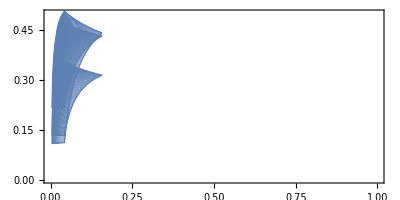

```mathematica
ParametricPlot[parplots, {λ1,10,30},{λ2,0,0.5},PlotRange->{{0, 1},{0,.5}}]
```

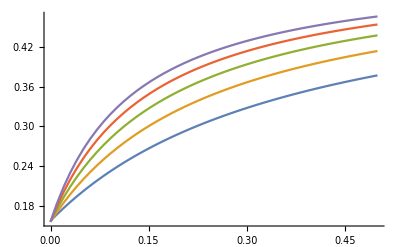

```mathematica
Plot[Evaluate[Table[Simplify[α/(αs ρ)/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,0.5}]
```

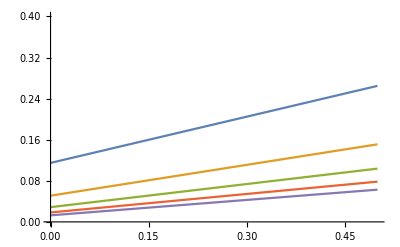

```mathematica
Plot[Evaluate[Table[Simplify[ρ/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,.5}, PlotRange->{0, 0.4}]
```